# sharp trap switching - F(x)

## begin with our most general expression for rhodt2 and use a gaussian switching function to find a less general expression for the | g > < g | transition probability

## the switching function

```mathematica
chiT1[t_]:=A/r*(t+c)
chiT2[t_]:=A
chiT3[t_]:=A/r*(c-t)
```

## the expression for the |g><g| probability, in 3 parts

#### the first interval

```mathematica
Integrate[chiT1[t]*ⅇ^(-ⅈ*(Abs[k]+Ω)*t),{t,-c-ϵ,-c}]
```

```mathematica
int1[t_]:=(A ⅇ^(ⅈ (c+ϵ) (Ω+Abs[k])) (-1+ⅇ^(-ⅈ ϵ (Ω+Abs[k]))+ⅈ ϵ Ω+ⅈ ϵ Abs[k]))/(ϵ (Ω+Abs[k])^2)
```

```mathematica
Integrate[chiT1[tp]*ⅇ^(ⅈ*(Abs[k]+Ω)*tp),{tp,-c-ϵ,-c}]
```

```mathematica
int2[tp_]:=(A ⅇ^(-ⅈ (c+ϵ) (Ω+Abs[k])) (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]))/(ϵ (Ω+Abs[k])^2)
```

```mathematica
Integrate[chiT1[t]*chiT1[tp]*Cos[Abs[k]*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c-ϵ,t}]
```

```mathematica
tpint[t_]:=1/(2 ϵ^2)A^2 (c+t) (1/(Ω-Abs[k])^2+1/(Ω+Abs[k])^2+(c Sin[(c+t+ϵ) (Ω-Abs[k])])/(Ω-Abs[k])-1/(Ω-Abs[k])^2(Cos[(c+t+ϵ) (Ω-Abs[k])]+(c+ϵ) Ω Sin[(c+t+ϵ) (Ω-Abs[k])]-(c+ϵ) Abs[k] Sin[(c+t+ϵ) (Ω-Abs[k])])+(c Sin[(c+t+ϵ) (Ω+Abs[k])])/(Ω+Abs[k])-1/(Ω+Abs[k])^2(Cos[(c+t+ϵ) (Ω+Abs[k])]+(c+ϵ) Ω Sin[(c+t+ϵ) (Ω+Abs[k])]+(c+ϵ) Abs[k] Sin[(c+t+ϵ) (Ω+Abs[k])]))
```

```mathematica
ggI1=A^2/(4*π*ϵ^2)*Integrate[ⅇ^(-ε*Abs[k])*Abs[k]*ftil[k]^2*
((1-α)*int1[t]*int2[tp]-
2*α*Integrate[tpint[t],{t,-c-ϵ,-c}])
,{k,-∞,∞}]
```

$Aborted

```mathematica
A^2/(4*π*ϵ^2)*Integrate[ⅇ^(-ε*Abs[k])*Abs[k]*ftil[k]^2*
(1-α)*int1[t]*int2[tp],{k,-∞,∞}]
```

(A^2 ∫_(-∞)^∞ (A^2 ⅇ^(-ε Abs[k]) (1-α) Abs[k] (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (-1+ⅇ^(-ⅈ ϵ (Ω+Abs[k]))+ⅈ ϵ Ω+ⅈ ϵ Abs[k]) ftil[k]^2)/(ϵ^2 (Ω+Abs[k])^4)ⅆk)/(4 π ϵ^2)

```mathematica
A^2/(4*π*ϵ^2)*Integrate[ⅇ^(-ε*Abs[k])*Abs[k]*ftil[k]^2*(-2)*α*Integrate[tpint[t],{t,-c-ϵ,-c},Assumptions->ϵ∈Reals&&ϵ>0&&Ω∈Reals]
,{k,-∞,∞}]
```

1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ -1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 ⅇ^(-ε Abs[k]) α Abs[k] ftil[k]^2 (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])ⅆk

```mathematica
ggI1=Out[10]+1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ 1/(ϵ^2 (Ω+Abs[k])^4)A^2 ⅇ^(-ε Abs[k]) (1-α) Abs[k] (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (-1+ⅇ^(-ⅈ ϵ (Ω+Abs[k]))+ⅈ ϵ Ω+ⅈ ϵ Abs[k]) ftil[k]^2 ⅆk
```

(A^2 ∫_(-∞)^∞ (A^2 ⅇ^(-ε Abs[k]) (1-α) Abs[k] (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (-1+ⅇ^(-ⅈ ϵ (Ω+Abs[k]))+ⅈ ϵ Ω+ⅈ ϵ Abs[k]) ftil[k]^2)/(ϵ^2 (Ω+Abs[k])^4)ⅆk)/(4 π ϵ^2)+1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ -1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 ⅇ^(-ε Abs[k]) α Abs[k] ftil[k]^2 (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])ⅆk

```mathematica
Simplify[%,Assumptions->ϵ∈Reals&&ϵ>0&&Ω∈Reals]
```

Undefined

#### the second interval

```mathematica
Integrate[chiT1[t]*ⅇ^(-ⅈ*(Abs[k]+Ω)*t),{t,-c-ϵ,-c}]
```

```mathematica
Integrate[chiT1[tp]*ⅇ^(ⅈ*(Abs[k]+Ω)*tp),{tp,-c-ϵ,-c}]
```

```mathematica
Integrate[chiT1[t]*chiT1[tp]*Cos[Abs[k]*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c-ϵ,t}]
```

```mathematica
ggI2=A^2/(4*π*ϵ^2)*Integrate[ⅇ^(-ε*Abs[k])*Abs[k]*ftil[k]^2*
((1-α)*Integrate[chiT2[t]*ⅇ^(-ⅈ*(Abs[k]+Ω)*t),{t,-c,c}]*Integrate[chiT2[tp]*ⅇ^(ⅈ*(Abs[k]+Ω)*tp),{tp,-c,c}]-
2*α*Integrate[Integrate[chiT2[t]*chiT2[tp]*Cos[Abs[k]*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c,t}],{t,-c,c}])
,{k,-∞,∞}]
```

1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ ⅇ^(-ε Abs[k]) Abs[k] ftil[k]^2 ((4 A^2 (1-α) Sin[c (Ω+Abs[k])]^2)/(Ω+Abs[k])^2-2 A^2 α (Sin[c (Ω-Abs[k])]^2/(Ω-Abs[k])^2+Sin[c (Ω+Abs[k])]^2/(Ω+Abs[k])^2))ⅆk

#### the third interval

```mathematica
ggI3=A^2/(4*π*ϵ^2)*Integrate[ⅇ^(-ε*Abs[k])*Abs[k]*ftil[k]^2*
((1-α)*Integrate[chiT3[t]*ⅇ^(-ⅈ*(Abs[k]+Ω)*t),{t,c,c+ϵ}]*Integrate[chiT3[tp]*ⅇ^(ⅈ*(Abs[k]+Ω)*tp),{tp,c,c+ϵ}]-
2*α*Integrate[Integrate[chiT3[t]*chiT3[tp]*Cos[Abs[k]*(t-tp)]*Cos[Ω*(t-tp)],{tp,c,t}],{t,c,c+ϵ}])
,{k,-∞,∞}]
```

1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ ⅇ^(-ε Abs[k]) Abs[k] ftil[k]^2 (1/(ϵ^2 (Ω+Abs[k])^4)A^2 ⅇ^(-ⅈ (c+ϵ) (Ω+Abs[k])) (1-α) (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (ⅇ^(ⅈ c (Ω+Abs[k]))+ⅈ ⅇ^(ⅈ (c+ϵ) (Ω+Abs[k])) (ⅈ+ϵ Ω+ϵ Abs[k]))-1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 α (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]]))ⅆk

#### add them together, hope something cancels

```mathematica
ggI1+ggI2+ggI3
```

(A^2 ∫_(-∞)^∞ (A^2 ⅇ^(-ε Abs[k]) (1-α) Abs[k] (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (-1+ⅇ^(-ⅈ ϵ (Ω+Abs[k]))+ⅈ ϵ Ω+ⅈ ϵ Abs[k]) ftil[k]^2)/(ϵ^2 (Ω+Abs[k])^4)ⅆk)/(4 π ϵ^2)+1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ -1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 ⅇ^(-ε Abs[k]) α Abs[k] ftil[k]^2 (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])ⅆk+1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ ⅇ^(-ε Abs[k]) Abs[k] ftil[k]^2 (1/(ϵ^2 (Ω+Abs[k])^4)A^2 ⅇ^(-ⅈ (c+ϵ) (Ω+Abs[k])) (1-α) (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (ⅇ^(ⅈ c (Ω+Abs[k]))+ⅈ ⅇ^(ⅈ (c+ϵ) (Ω+Abs[k])) (ⅈ+ϵ Ω+ϵ Abs[k]))-1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 α (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]]))ⅆk+1/(4 π ϵ^2)A^2 ∫_(-∞)^∞ ⅇ^(-ε Abs[k]) Abs[k] ftil[k]^2 ((4 A^2 (1-α) Sin[c (Ω+Abs[k])]^2)/(Ω+Abs[k])^2-2 A^2 α (Sin[c (Ω-Abs[k])]^2/(Ω-Abs[k])^2+Sin[c (Ω+Abs[k])]^2/(Ω+Abs[k])^2))ⅆk

```mathematica
(1/(ϵ^2 (Ω+Abs[k])^4)A^2 ⅇ^(-ⅈ (c+ϵ) (Ω+Abs[k])) (1-α) (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (ⅇ^(ⅈ c (Ω+Abs[k]))+ⅈ ⅇ^(ⅈ (c+ϵ) (Ω+Abs[k])) (ⅈ+ϵ Ω+ϵ Abs[k]))-1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 α (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]]))+(ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])(-1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2) + ((4 A^2 (1-α) Sin[c (Ω+Abs[k])]^2)/(Ω+Abs[k])^2-2 A^2 α (Sin[c (Ω-Abs[k])]^2/(Ω-Abs[k])^2+Sin[c (Ω+Abs[k])]^2/(Ω+Abs[k])^2))
```

```mathematica
Simplify[1/(ϵ^2 (Ω+Abs[k])^4)A^2 ⅇ^(-ⅈ (c+ϵ) (Ω+Abs[k])) (1-α) (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (ⅇ^(ⅈ c (Ω+Abs[k]))+ⅈ ⅇ^(ⅈ (c+ϵ) (Ω+Abs[k])) (ⅈ+ϵ Ω+ϵ Abs[k]))-1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])-1/(ϵ^2 (Ω^2-Abs[k]^2)^4)A^2 α (ϵ^2 Abs[k]^6+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-Ω^2 Abs[k]^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+Abs[k]^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])+(4 A^2 (1-α) Sin[c (Ω+Abs[k])]^2)/(Ω+Abs[k])^2-2 A^2 α (Sin[c (Ω-Abs[k])]^2/(Ω-Abs[k])^2+Sin[c (Ω+Abs[k])]^2/(Ω+Abs[k])^2),Assumptions->ϵ∈Reals&&ϵ>0&&c∈Reals&&c>0&&Ω∈Reals&&k∈Reals]
```

A^2 (1/(ϵ^2 (Ω+Abs[k])^4)ⅇ^(-ⅈ (c+ϵ) (Ω+Abs[k])) (1-α) (-1+ⅇ^(ⅈ ϵ (Ω+Abs[k]))-ⅈ ϵ Ω-ⅈ ϵ Abs[k]) (ⅇ^(ⅈ c (Ω+Abs[k]))+ⅈ ⅇ^(ⅈ (c+ϵ) (Ω+Abs[k])) (ⅈ+ϵ Ω+ϵ Abs[k]))-1/(ϵ^2 (k^2-Ω^2)^4)α (k^6 ϵ^2+Ω^4 (2+ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]-2 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-k^2 Ω^2 (-12+ϵ^2 Ω^2+12 Cos[ϵ Ω] Cos[ϵ Abs[k]]+4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])+k^4 (2-ϵ^2 Ω^2-2 Cos[ϵ Ω] Cos[ϵ Abs[k]]+6 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω])-2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]+2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]-4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])+1/(ϵ^2 (k^2-Ω^2)^4)(-2 k^4-k^6 ϵ^2-12 k^2 Ω^2+k^4 ϵ^2 Ω^2-2 Ω^4+k^2 ϵ^2 Ω^4-ϵ^2 Ω^6+2 (k^4+6 k^2 Ω^2+Ω^4) Cos[ϵ Ω] Cos[ϵ Abs[k]]-6 k^4 ϵ Ω Cos[ϵ Abs[k]] Sin[ϵ Ω]+4 k^2 ϵ Ω^3 Cos[ϵ Abs[k]] Sin[ϵ Ω]+2 ϵ Ω^5 Cos[ϵ Abs[k]] Sin[ϵ Ω]+2 ϵ Abs[k]^5 Cos[ϵ Ω] Sin[ϵ Abs[k]]-2 Ω^3 Abs[k] (3 ϵ Ω Cos[ϵ Ω]-4 Sin[ϵ Ω]) Sin[ϵ Abs[k]]+4 Ω Abs[k]^3 (ϵ Ω Cos[ϵ Ω]+2 Sin[ϵ Ω]) Sin[ϵ Abs[k]])-(4 (-1+α) Sin[c (Ω+Abs[k])]^2)/(Ω+Abs[k])^2-2 α (Sin[c (Ω-Abs[k])]^2/(Ω-Abs[k])^2+Sin[c (Ω+Abs[k])]^2/(Ω+Abs[k])^2))

```mathematica
Expand[%]
```

True

```mathematica
ggintegrand[k_]:=ⅇ^(-ε k) k ftil[k]^2 A^4/(2π*ϵ^2)*((1/(ϵ^2 (Ω+k)^4)ⅇ^(-ⅈ (c+ϵ) (Ω+k)) (1-α) (-1+ⅇ^(ⅈ ϵ (Ω+k))-ⅈ ϵ *Ω-ⅈ ϵ* k) (ⅇ^(ⅈ c (Ω+k))+ⅈ ⅇ^(ⅈ (c+ϵ) (Ω+k)) (ⅈ+ϵ( Ω+k))))+(1-α)/(ϵ^2 (k^2-Ω^2)^4)(-k^6 ϵ^2-k^4(-2+ϵ^2 Ω^2)+k^2(ϵ^2 Ω^4-12 Ω^2)-2 Ω^4-ϵ^2 Ω^6+2 (k^4+6 k^2 Ω^2+Ω^4) Cos[ϵ Ω] Cos[ϵ *k]-(6 k^4 ϵ Ω +4 k^2 ϵ Ω^3 +2 ϵ Ω^5 )Cos[ϵ*k] Sin[ϵ Ω]+((2 ϵ *k^5 -6 Ω^4 k* ϵ +4 Ω^2 k^3 ϵ ) Cos[ϵ Ω]+(8 Ω^3+8Ω *k^3)Sin[ϵ Ω]) Sin[ϵ *k])+((4-6α) Sin[c (Ω+k)]^2)/(Ω+k)^2-2α Sin[c (Ω-k)]^2/(Ω-k)^2)
```

note before here ϵ = r

```mathematica
gg=Integrate[ggintegrand[k],{k,0,∞}]
```

```mathematica
∫_0^∞ 1/(2 π r^2)A^4 ⅇ^(-k ε) k ftil[k]^2 ((ⅇ^(-ⅈ (c+ϵ) (k+Ω)) (1-α) (-1+ⅇ^(ⅈ ϵ (k+Ω))-ⅈ k r-ⅈ r Ω) (ⅇ^(ⅈ c (k+Ω))+ⅈ ⅇ^(ⅈ (c+ϵ) (k+Ω)) (ⅈ+r (k+Ω))))/(r^2 (k+Ω)^4)+1/(r^2 (k^2-Ω^2)^4)(1-α) (-k^6 r^2-2 Ω^4-r^2 Ω^6-k^4 (-2+r^2 Ω^2)+k^2 (-12 Ω^2+r^2 Ω^4)+2 (k^4+6 k^2 Ω^2+Ω^4) Cos[k r] Cos[r Ω]-(6 k^4 r Ω+4 k^2 r Ω^3+2 r Ω^5) Cos[k r] Sin[r Ω]+Sin[k r] ((2 k^5 r+4 k^3 r Ω^2-6 k r Ω^4) Cos[r Ω]+(8 k^3 Ω+8 Ω^3) Sin[r Ω]))-(2 α Sin[c (-k+Ω)]^2)/(-k+Ω)^2+((4-6 α) Sin[c (k+Ω)]^2)/(k+Ω)^2)ⅆk
```

## plot this as a function of k

#### set parameters

```mathematica
c=1;r=0.2;ε=0.25;Ω=1;A=1/(ϵ+2*c);α=1;σ=1;
```

#### clear params

```mathematica
Clear[c,ϵ,ε,Ω,A,α,σ]
```

#### plot

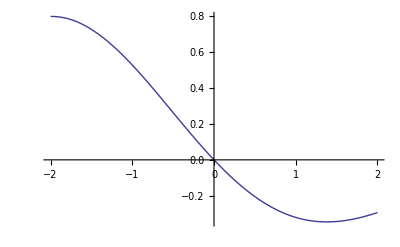

```mathematica
Plot[ggintegrand[k]/ftil[k]^2,{k,-2,2}]
```

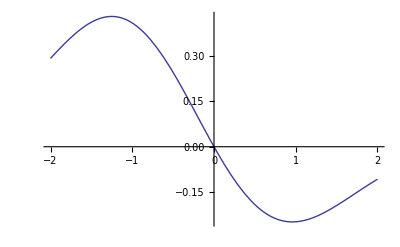

```mathematica
Plot[ggintegrand[k]/ftil[k]^2*ⅇ^(-1/4 k^2 σ^2),{k,-2,2}]
```

## the k integrand from the ground state

```mathematica
ggintegrandgd[k_]:=(A^4 ⅇ^(-k ε) k ftil[k]^2 (-(2 Sin[c (-k+Ω)]^2)/(-k+Ω)^2-(2 Sin[c (k+Ω)]^2)/(k+Ω)^2))/(2 π r^2)
```